# Minstakvadratmetoden

## Exempel från föreläsningen

### Exempel 1

f(x,p) = 0.8+1.2 x

Jämför med Mathematicas funktion Fit: 0.8+1.2 x

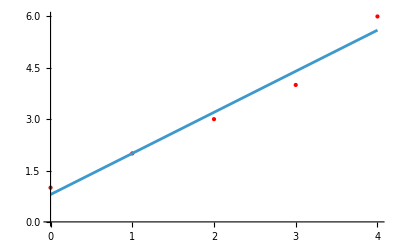

```mathematica
Remove["Global`*"]
xv={0,1,2,3,4};
y={1,2,3,4,6};
data=Transpose[{xv,y}];
nmax=Length[xv];
a=Transpose[{xv,Table[1,{i,1,nmax}]}];
p={k,m};
f={x,1}.p;
sol=Solve[Transpose[a].a.p==Transpose[a].y,p];
Print["f(x,p) = ",N[f/.sol[[1]]]]
pl=Plot[f/.sol[[1]],{x,xv[[1]],xv[[nmax]]}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Print["Jämför med Mathematicas funktion Fit: ",Fit[data,{1,x},x]]
Show[lp,pl]
```

### Exempel 5

f(x,p) = 3.02857-1.65714 x+0.714286 x^2

Jämför med Mathematicas funktion Fit: 3.02857-1.65714 x+0.714286 x^2

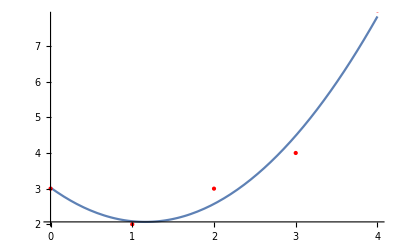

```mathematica
Remove["Global`*"]
xv={0,1,2,3,4};
y={3,2,3,4,8};
xv2=xv^2;
n=Length[xv];
a=Transpose[{xv2,xv,Table[1,{i,1,n}]}];
deg=2;
p=Reverse[Table[c[i],{i,0,deg}]];
f=Reverse[Table[x^(i),{i,0,deg}]].p;
data=Transpose[{xv,y}];
sol=Solve[Transpose[a].a.p==Transpose[a].y,p];
Print["f(x,p) = ",N[f/.sol[[1]]]]
Print["Jämför med Mathematicas funktion Fit: ",Fit[data,{1,x,x^2},x]]
pl=Plot[f/.sol[[1]],{x,xv[[1]],xv[[n]]}];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Show[pl,lp]
```

### Exempel 6

f(x,p) = 0.0364643+0.552146 x

Jämför med Mathematicas funktion Fit: 0.0364643+0.552146 x

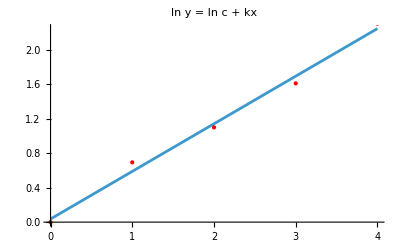

c = 1.03714

k = 0.552146

Jämför med Mathematicas funktion FindFit: {cc→0.901465,kk→0.597711}

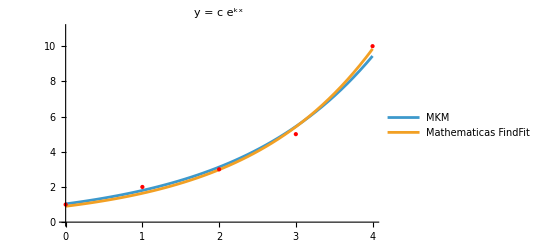

```mathematica
Remove["Global`*"]
xv={0,1,2,3,4};
yv={1,2,3,5,10};
y=Log[yv];
n=Length[xv];
a=Transpose[{xv,Table[1,{i,1,n}]}];
deg=1;
p=Reverse[Table[c[i],{i,0,deg}]];
f=Reverse[Table[x^(i),{i,0,deg}]].p;
data=Transpose[{xv,y}];
sol=Solve[Transpose[a].a.p==Transpose[a].y,p];
Print["f(x,p) = ",N[f/.sol[[1]]]]
Print["Jämför med Mathematicas funktion Fit: ",Fit[data,{1,x},x]]
pl=Plot[f/.sol[[1]],{x,xv[[1]],xv[[n]]},PlotLabel->"ln y = ln c + kx"];
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
Show[pl,lp]
Print["c = ",c=N[Exp[c[0]]/.sol[[1]]]]
Print["k = ",k=N[c[1]/.sol[[1]]]]
data2=Transpose[{xv,yv}];
Print["Jämför med Mathematicas funktion FindFit: ",fit=FindFit[data2,cc*Exp[kk*x],{cc,kk},x]]
pl=Plot[{c*Exp[k*x],(cc*Exp[kk*x]/.fit)},{x,xv[[1]],xv[[n]]},
PlotRange->{0,11},
PlotLabel->"y = c e^kx",
PlotLegends->Placed[{"MKM","Mathematicas FindFit"},{0.3,0.9}]
];
lp=ListPlot[data2,PlotStyle->{Red,PointSize[Large]}];
Show[pl,lp]
```

### Exempel 7

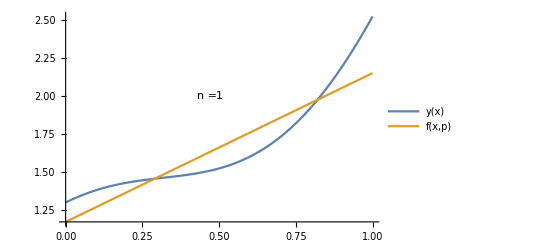

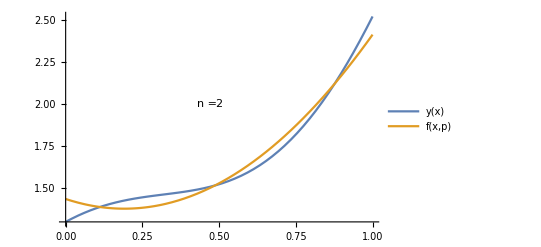

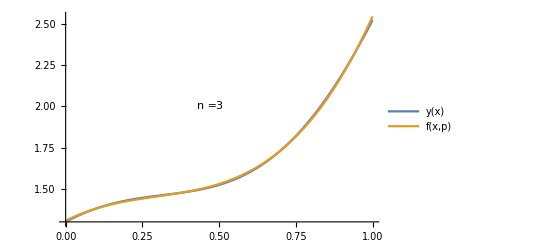

```mathematica
Remove["Global`*"]
y[x_]=0.3Cos[4x]+Exp[x];
n=3; (* Max grad på p *)
For[k=1,k<=n,k++,
p=Table[c[i],{i,0,k}];
f[x_]=Table[x^i,{i,0,k}].p;
s=Integrate[(f[x]-y[x])^2,{x,0,1}];
sol=Solve[D[s,{p}]==0,p];
Plot[{y[x],f[x]/.sol[[1]]},{x,0,1},
PlotLegends->{"y(x)","f(x,p)"},
Epilog->{Text["n = ",{0.46,2}],Text[k,{0.5,2}]}]//Print
]
```